### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(*Some unimportant error messages are sw
itched off for future convenience*)
Off[NIntegrate::inumr,FindRoot::lstol,NIntegrate::ncvb];
```

### Various Constants

```mathematica
(* The Subscript[Ω, b] h^2 value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
obh2pl=0.02236;
(* The Subscript[Ω, m] value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
ompl=0.3166;
(* The Subscript[H, 0] value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
H0pl=67.27;
(* The dimensionless parameter for the Hubble constant, defined as Subscript[H, 0]/100 *)
h0pl=H0pl/100;
(* The h value from Type Ia Supernovae - See abstract of https://arxiv.org/pdf/1903.07603.pdf *)
h0riess=0.7403;
(* CMB temperature *)
Tcmb=2.7255;
(* Various constants useful for the following likelihoods *)
c=299792.458;
cH0=2997.92458;
```

### nCPL Model

#### χ^2 Analysis

```mathematica
(* w(a)=Subscript[w, 0]-(Subscript[w, a](1-a))^n, i.e. nCPL model - For n=1 we get the usual CPL model *)
w[a_,w0_,wa_,n_]:=w0+wa (1-a)^n
(* Subscript[f, DE](α) for the nCPL model - See Eq. (4.2) on page 12 from https://arxiv.org/pdf/1603.02164.pdf *)
f[a_,w0_,wa_,n_]:=a^(-3 (1+w0+wa)) ⅇ^(-3 wa HarmonicNumber[n]+3 a n wa HypergeometricPFQ[{1,1,1-n},{2,2},a])
(* Define Subscript[z, equality] and Subscript[a, equality] in order to avoid some problems *)
zeq[om_?NumberQ,h_?NumberQ]:=2.5*10^4 om h^2 (Tcmb/2.7)^-4;
aeq[om_?NumberQ,h_?NumberQ]:=1/(1+zeq[om,h]);
(* E=H/H0 for the nCPL model - See Eq. (4.3) on page 12 from https://arxiv.org/pdf/1603.02164.pdf*) 
H[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=100h Sqrt[a^-3 om(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))f[a,w0,wa,n]]
(* Sound speed - Easily proved from Eq. (3.2) of https://arxiv.org/pdf/1812.05356.pdf *) 
cs[a_?NumberQ,obh2_?NumberQ]:=c/(√(3(1+(31500 obh2(Tcmb/2.7)^-4)a) ));
(* Redshift at decoupling - See Eqs. (E-1) on page 33 or see Eqs. (66)-(68) of https://arxiv.org/pdf/0803.0547.pdf on page 30 *)
zcmb[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1048(1+0.00124(obh2)^-0.738)(1+((0.0783(obh2)^-0.238)/(1+39.5(obh2)^0.763))(om h^2)^(0.560/(1+21.1(obh2)^1.81)))
(* Drag redshift - See Eqs. (4) of https://arxiv.org/pdf/astro-ph/9709112.pdf on page 5 *)
zdrag[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1291 ((om h^2)^0.251/(1+0.659 (om h^2)^0.828))(1+(0.313(om h^2)^-0.419(1+0.607(om h^2)^0.674))(obh2)^(0.238(om h^2)^0.223))
(* Comoving sound horizon at drag redshift - Easily proved from Eq. (3.1) of https://arxiv.org/pdf/1812.05356.pdf *)
rs[ze_,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=NIntegrate[cs[x,obh2]/(x^2H[x,om,w0,wa,n,h]),{x,10^-11,1/(1+ze[om,obh2,h])}]
(* Luminosity distance Subscript[d, L]- See e.g. Eq. (1.2) from https://arxiv.org/pdf/2004.02155.pdf on page 2 - Define it as it is due to some problems! *)
Clear[DLsol,DL,dL]
DLsol[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(DLsol[om,w0,wa,n,h]=NDSolve[{D[dL[zz]/(1+zz),zz]==1/(H[1/(1+zz),om,w0,wa,n,h]/(100h)),dL[0]==0},dL,{zz,0,1300},MaxSteps->Infinity])
DL[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=((c/(100h))dL[z]/.DLsol[om,w0,wa,n,h])[[1]]//Chop
(* Angular diameter distance Subscript[d, A] *)
DA[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=DL[z,om,w0,wa,n,h]/(1+z)^2
(* Easily proven from Eq. (3.4) of https://arxiv.org/pdf/1812.05356.pdf *)
Dv[zbao_,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=((DL[zbao,om,w0,wa,n,h] /(1+zbao))^2  ((c*zbao)/H[1/(1+zbao),om,w0,wa,n,h]))^(1/3)
(* BAO Subscript[d, z] ratio - Subscript[d, z]=Subscript[r, s]/Subscript[D, V] *)
dz[zbao_,om_,obh2_,w0_,wa_,n_,h_]:=rs[zdrag,om,obh2,w0,wa,n,h]/Dv[zbao,om,w0,wa,n,h]
(* Subscript[D, H] "distance" defined as Subscript[D, H](z)=c/(H(z)) - See the end of page 8 from https://arxiv.org/pdf/1812.05356.pdf *)
DH[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=c/H[1/(1+z),om,w0,wa,n,h]
hz[z_,om_,w0_,wa_,n_,h_]:=H[1/(1+z),om,w0,wa,n,h]
(* Comoving distance at recombination - Easily proven from Eq. (26) of https://arxiv.org/pdf/1811.07425.pdf on page 7 *)
R[om_,obh2_,w0_,wa_,n_,h_]:=(√(om (100h)^2)DA[zcmb[om,obh2,h],om,w0,wa,n,h](1+zcmb[om,obh2,h]))/c
(* Angular scale of sound horizon at recombination - Easily proven from Eq. (27) of https://arxiv.org/pdf/1811.07425.pdf on page 7  *)
la[om_,obh2_,w0_,wa_,n_,h_]:=(π (DA[zcmb[om,obh2,h],om,w0,wa,n,h](1+zcmb[om,obh2,h])))/rs[zcmb,om,obh2,w0,wa,n,h]
```

### Data Combination

#### CMB Data

```mathematica
(* Central values for {R, Subscript[l, a], Subscript[Ω, b] h^2} from Planck 2018 for a flat universe - See Eq. (31) of https://arxiv.org/pdf/1811.07425.pdf on page 7 *)
datacmb={1.74963,301.80845,0.02237};
(* Inverse Covariance Matrix using  for {R, Subscript[l, a], Subscript[Ω, b] h^2} *)
covcmb=10^-8({{1598.9554, 17112.007, −36.311179}, {17112.007, 811208.45, −494.79813}, {-36.311179, -494.79813, 2.1242182}});
invcov=Inverse[covcmb];
ndatCMB=Length[datacmb];
(* χ^2 for CMB shift parameters *)
vec[om_,obh2_,w0_,wa_,n_,h_]:={R[om,obh2,w0,wa,n,h]-datacmb[[1]],la[om,obh2,w0,wa,n,h]-datacmb[[2]],obh2-datacmb[[3]]};
chi2R[om_,obh2_,w0_,wa_,n_,h_]:=vec[om,obh2,w0,wa,n,h].invcov.vec[om,obh2,w0,wa,n,h]
```

#### BAO Data

```mathematica
(* 6dFGs and WiggleZ BAO measurements - See page 6 of https://arxiv.org/pdf/1605.02702.pdf *)
databao={{0.106,0.336,0.015},{0.44,0.073,0.031},{0.6,0.0726,0.0164},{0.73,0.0592,0.0185}};
Cijbaoinv=({{1/databao[[1,3]]^2, 0, 0, 0}, {0, 1040.3, -807.5, 336.8}, {0, -807.5, 3720.3, -1551.9}, {0, 336.8, -1551.9, 2914.9}});
(* V^i crucial for the construction of this subset of the BAO χ^2 *)
vecbao[om_,obh2_,w0_,wa_,n_,h_]:=Table[(databao[[i,2]]-dz[databao[[i,1]],om,obh2,w0,wa,n,h]),{i,1,Length[databao]}];
```

```mathematica
(* SDSS BAO measurements from Data Release (DR) 7 and DR11. These measurements correspond to (Dv/Subscript[r, d])=Dv/Subscript[r, s] - See abstract of http://arxiv.org/abs/1409.3242 and of https://arxiv.org/abs/1312.4877 respectively *)
dataSDSS={{0.15,4.465666824,0.1681350461},{0.32,8.4673,0.167},{0.57,13.7728,0.134}};
```

```mathematica
(* Ly-α BAO measurements. The first one corresponds to (Subscript[D, A]/Subscript[r, d])=(Subscript[D, A]/Subscript[r, s]) while the second one to (Subscript[D, H]/Subscript[r, d])=Subscript[D, H]/Subscript[r, s] - See abstract of https://arxiv.org/abs/1904.03400 *)
dataLya={{2.34,11.2005988024,0.56},{2.34,8.86,0.29}};
CijLyainv=({{1/dataLya[[1,3]]^2, 0}, {0, 1/dataLya[[2,3]]^2}});
(* χ^2 for the Ly-α BAO measurements *)
vecLya[om_,obh2_,w0_,wa_,n_,h_]:={dataLya[[1,2]]-DA[dataLya[[1,1]],om,w0,wa,n,h]/rs[zdrag,om,obh2,w0,wa,n,h],dataLya[[2,2]]-DH[dataLya[[2,1]],om,w0,wa,n,h]/rs[zdrag,om,obh2,w0,wa,n,h]};
(* Length of the BAO data *)
ndatBAO=Length[dataSDSS]+Length[databao]+Length[dataLya];
```

```mathematica
(* Total BAO χ^2 *)
chi2bao[om_,obh2_,w0_,wa_,n_,h_]:=vecbao[om,obh2,w0,wa,n,h].Cijbaoinv.vecbao[om,obh2,w0,wa,n,h]+Sum[(dataSDSS[[i,2]]-1/dz[dataSDSS[[i,1]],om,obh2,w0,wa,n,h])^2/dataSDSS[[i,3]]^2,{i,1,Length[dataSDSS]}]+vecLya[om,obh2,w0,wa,n,h].CijLyainv.vecLya[om,obh2,w0,wa,n,h]
```

#### Full Pantheon Data

```mathematica
(* Import the full Pantheon data. The full (as well as the binned Pantheon) data can be found in https://github.com/dscolnic/Pantheon. Short descriptions in https://archive.stsci.edu/prepds/ps1cosmo/index.html as well as in https://arxiv.org/abs/1710.00845 *)
dataPanth=Import[".\\data\\lcparam_full_long_zhel.txt","Table"];
(* Length of Pantheon data *)
ndatPanth=Length[dataPanth]-1;
(* Import the systematic errors which are in a separate file *)
Dij0=Import[".\\data\\sys_full_long.txt","List"];
Dij=Partition[Dij0[[2;;-1]],{Dij0[[1]]}];
Id=ConstantArray[1,ndatPanth];
(* Construct of the covariance using only the statistical uncertainties *)
Covstat=DiagonalMatrix[dataPanth[[All,6]][[2;;-1]]^2];
(* Construct of the covariance using only the systematic uncertainties *)
Covsys=Dij;
(* Add the two matrices to construct the total one *)
```

```mathematica
Cijtot=Covsys+Covstat;
InvCovTotal=Inverse[Cijtot];
InvCovstat=Inverse[Covstat];
```

```mathematica
(* χ^2 for the Pantheon data. For the theoretical expression of the apparent magnitude m see my Msc diploma thesis as well as Section 2 of https://arxiv.org/pdf/2004.02155.pdf, where we extensively discuss the Pantheon dataset - IMPORTANT: If you want to rewritte the likelihood as a function of ℳ (as discussed in https://arxiv.org/pdf/2004.02155.pdf) you should redefine H function above to avoid some problems (ask me how to do that!) *)
chi2Panth[M_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=
Module[{Δm},
Δm=Table[dataPanth[[1+i,5]]-(M+5 Log10[((1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]]))DL[dataPanth[[1+i,2]],om,w0,wa,n,h]]+25),{i,1,ndatPanth}];
Δm.InvCovTotal.Δm]
```

### Total χ^2

#### χ^2 for ΛCDM, wCDM and CPL models

```mathematica
(* Subscript[χ, tot]^2=Subscript[χ, CMB]^2+Subscript[χ, BAO]^2+Subscript[χ, Panth]^2 - Similarly you can add as many likelihoods as you want! *)
chi2total[M_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=chi2R[om,obh2pl,w0,wa,1,h]+chi2bao[om,obh2pl,w0,wa,1,h]+ chi2Panth[M,om,w0,wa,1,h]
(* Total Length of the data *)
ndatot=ndatCMB+ndatBAO+ndatPanth
```

1060

```mathematica
(* χ^2 for the ΛCDM model using all three likelihoods *)
minlcdm=FindMinimum[chi2total[M,om,-1,0,h],{M,-19,-19.1},{om,0.32,0.321},{h,0.67,0.671}]
```

{1032.71,{M→-19.4294,om→0.316912,h→0.672379}}

```mathematica
Mlcdm = minlcdm[[2,1,2]];
omlcdm = minlcdm[[2,2,2]];
wolcdm = -1;
walcdm  = 0;
hlcdm = minlcdm[[2,3,2]];
```

```mathematica
(* χ^2 for the wCDM model using all three likelihoods *)
minwwcdm=FindMinimum[chi2total[M,om,w0,0,h],{M,-19,-19.1},{om,0.32,0.321},{w0,-1.,-1.1},{h,0.67,0.671}]
```

{1032.6,{M→-19.424,om→0.314726,w0→-1.01074,h→0.675026}}

```mathematica
Mwwcdm = minwwcdm[[2,1,2]];
omwwcdm = minwwcdm[[2,2,2]];
wowwcdm = minwwcdm[[2,3,2]];
wawwcdm  = 0;
hwwcdm = minwwcdm[[2,4,2]];
```

## Riess Point

```mathematica
chi2riessh[h_?NumberQ] := (h-h0riess)^2/(0.0142)^2
```

```mathematica
chi2total5[M_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=chi2R[om,obh2pl,w0,wa,1,h]+chi2bao[om,obh2pl,w0,wa,1,h]+ chi2Panth[M,om,w0,wa,1,h]+chi2riessh[h]
```

```mathematica
minwcdmriess= FindMinimum[chi2total5[M,om,w0,0,h],{M,-19,-19.1},{om,0.28,0.29},{w0,-1.2,-0.8},{h,0.67,0.7}]
```

{1047.86,{M→-19.3866,om→0.298659,w0→-1.07411,h→0.693301}}

```mathematica
Mwcdm = minwcdmriess[[2,1,2]];
omwcdm = minwcdmriess[[2,2,2]];
wowcdm = minwcdmriess[[2,3,2]];
wawcdm  = 0;
hwcdm = minwcdmriess[[2,4,2]]
```

0.693301

## dchi

```mathematica
dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
```

## WCDM

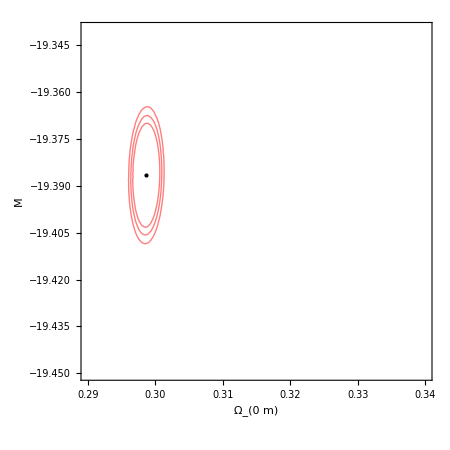

```mathematica
contour1 =ContourPlot[chi2total[M,om,wowcdm,wawcdm,hwcdm],{om,0.29,0.34},{M,-19.34,-19.45},Contours->{minwcdmriess[[1]]+dchi[1,4],minwcdmriess[[1]]+dchi[2,4],minwcdmriess[[1]]+dchi[3,4]},FrameLabel->{"Ω_(0  m)","M"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{omwcdm,Mwcdm}]}},ContourShading->False,ContourStyle->Red,ImageSize->450]
```

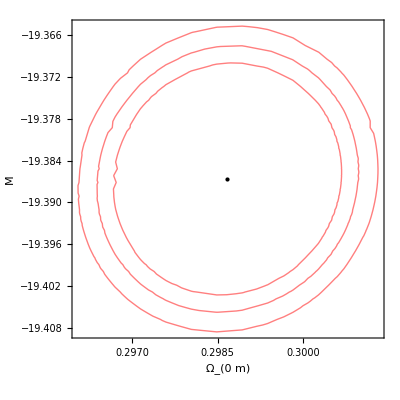

```mathematica
plt1 = Show[contour1,PlotRange->{{0.27,0.34},{-19.36,-19.42}},ImageSize->400,BaseStyle->{FontFamily->"Times",18}]
```

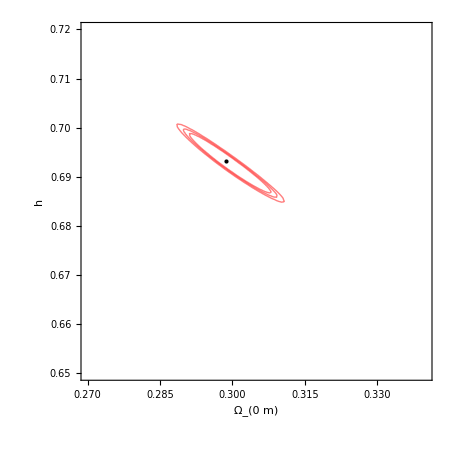

```mathematica
contour2 =ContourPlot[chi2total[Mwcdm,om,wowcdm,wawcdm,h],{om,0.27,0.34},{h,0.65,0.72},Contours->{minwcdmriess[[1]]+dchi[1,4],minwcdmriess[[1]]+dchi[2,4],minwcdmriess[[1]]+dchi[3,4]},FrameLabel->{"Ω_(0  m)","h"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{omwcdm,hwcdm}]}},ContourShading->False,ContourStyle->Red,ImageSize->450]
```

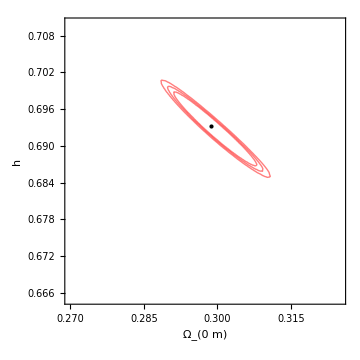

```mathematica
plt2 = Show[contour2,PlotRange->{{0.27,0.325},{0.665,0.71}},AspectRatio->1,PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",14},FrameStyle->Directive[Black],Frame->{{True,True},{True,True}}]
```

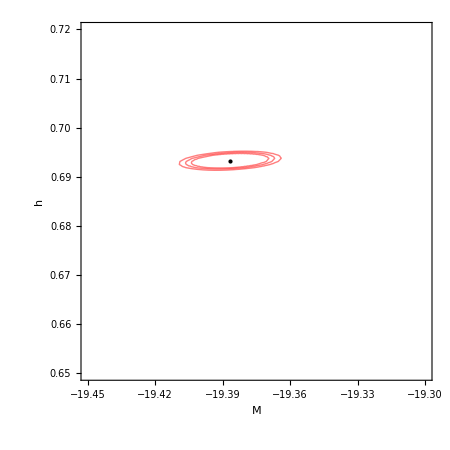

```mathematica
contour3 =ContourPlot[chi2total[M,omwcdm,wowcdm,wawcdm,h],{M,-19.3,-19.45},{h,0.65,0.72},Contours->{minwcdmriess[[1]]+dchi[1,4],minwcdmriess[[1]]+dchi[2,4],minwcdmriess[[1]]+dchi[3,4]},FrameLabel->{"M","h"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{Mwcdm,hwcdm}]}},ContourShading->False,ContourStyle->Red,ImageSize->450]
```

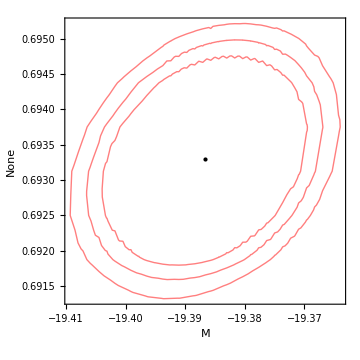

```mathematica
plt3= Show[contour3,PlotRange->{{-19.36,-19.45},{0.65,0.715}},AspectRatio->1,Frame->{{False,True},{True,True}},FrameLabel->{"M","None"},PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",14},FrameStyle->Directive[Black],ImagePadding->{{Automatic, 50}, {Automatic, 20}}]
```

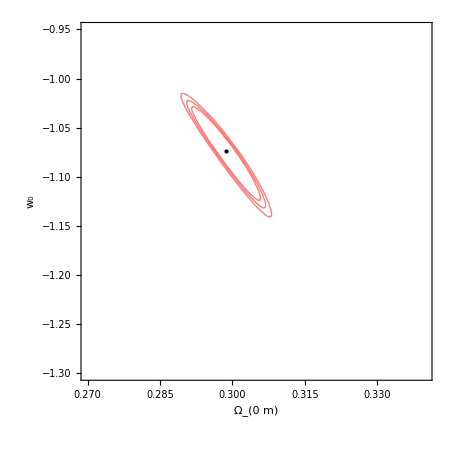

```mathematica
contour4 =ContourPlot[chi2total[Mwcdm,om,w0,wawcdm,hwcdm],{om,0.27,0.34},{w0,-1.30,-0.95},Contours->{minwcdmriess[[1]]+dchi[1,4],minwcdmriess[[1]]+dchi[2,4],minwcdmriess[[1]]+dchi[3,4]},FrameLabel->{"Ω_(0  m)","w_0"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{omwcdm,wowcdm}]}},ContourShading->False,ContourStyle->Red,ImageSize->450]
```

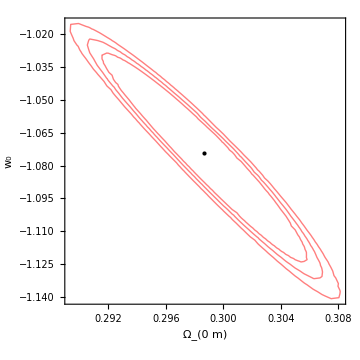

```mathematica
plt4 = Show[contour4,PlotRange->{{0.27,0.325},{-0.95,-1.3}},AspectRatio->1,PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",14},FrameStyle->Directive[Black],Frame->{{True,True},{True,True}}]
```

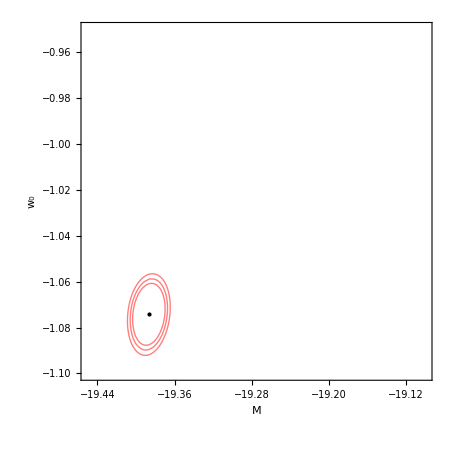

```mathematica
contour5 =ContourPlot[chi2total[M,omwcdm,w0,wawcdm,hwcdm],{M,-19.1,-19.45},{w0,-1.10,-0.95},Contours->{minwcdmriess[[1]]+dchi[1,4],minwcdmriess[[1]]+dchi[2,4],minwcdmriess[[1]]+dchi[3,4]},FrameLabel->{"M","w_0"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{Mwcdm,wowcdm}]}},ContourShading->False,ContourStyle->Red,ImageSize->450]
```

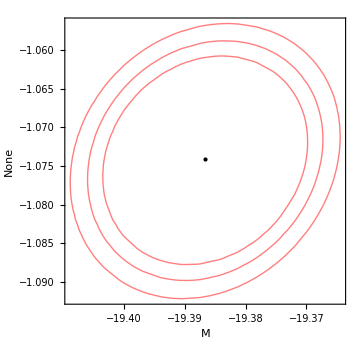

```mathematica
plt5 = Show[contour5,PlotRange->{{-19.35,-19.45},{-0.95,-1.3}},AspectRatio->1,Frame->{{False,True},{True,True}},FrameLabel->{"M","None"},PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",14},FrameStyle->Directive[Black],ImagePadding->{{Automatic, Automatic}, {Automatic, 10}}]
```

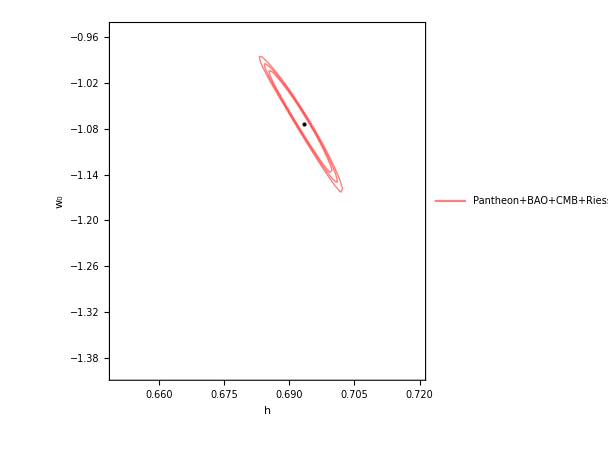

```mathematica
contour6 =ContourPlot[chi2total[Mwcdm,omwcdm,w0,wawcdm,h],{h,0.65,0.72},{w0,-1.40,-0.95},Contours->{minwcdmriess[[1]]+dchi[1,4],minwcdmriess[[1]]+dchi[2,4],minwcdmriess[[1]]+dchi[3,4]},FrameLabel->{"h","w_0"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{hwcdm,wowcdm}]}},ContourShading->False,ContourStyle->Red,ImageSize->450,PlotLegends->Placed[{"Pantheon+BAO+CMB+Riess"},{Right,Bottom}]]
```

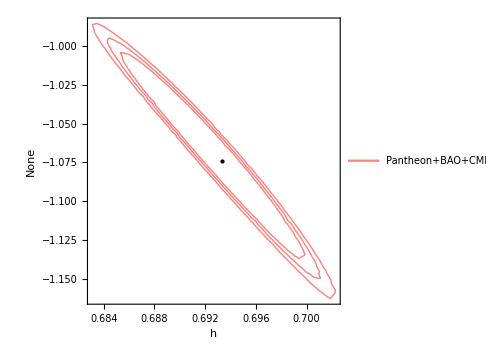

```mathematica
plt6 = Show[contour6,PlotRange->{{0.65,0.715},{-0.95,-1.3}},AspectRatio->1,Frame->{{False,True},{True,True}},FrameLabel->{"h","None"},PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",14},FrameStyle->Directive[Black],ImagePadding->{{Automatic, 50}, {Automatic, 20}}]
```

```mathematica
fig4=GraphicsGrid[{{plt1},{plt2,plt3},{plt4,plt5,plt6}},Spacings->-52,ImageSize->1150];
```

```mathematica
plt1
```

-Graphics-

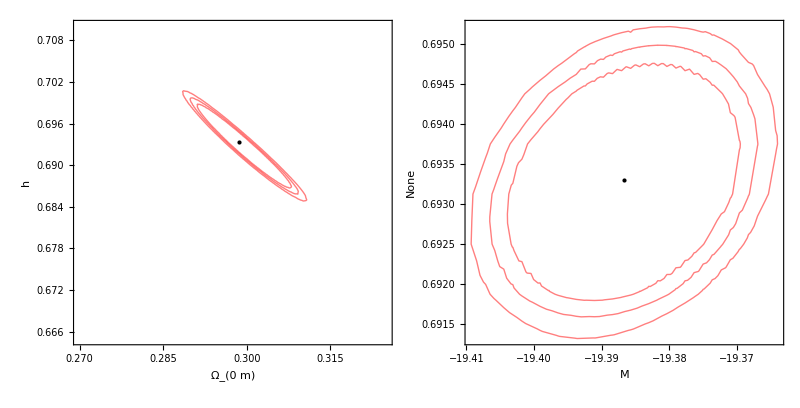

```mathematica
fig7=GraphicsGrid[{{plt2,plt3}},Spacings->-15,ImageSize->800]
```

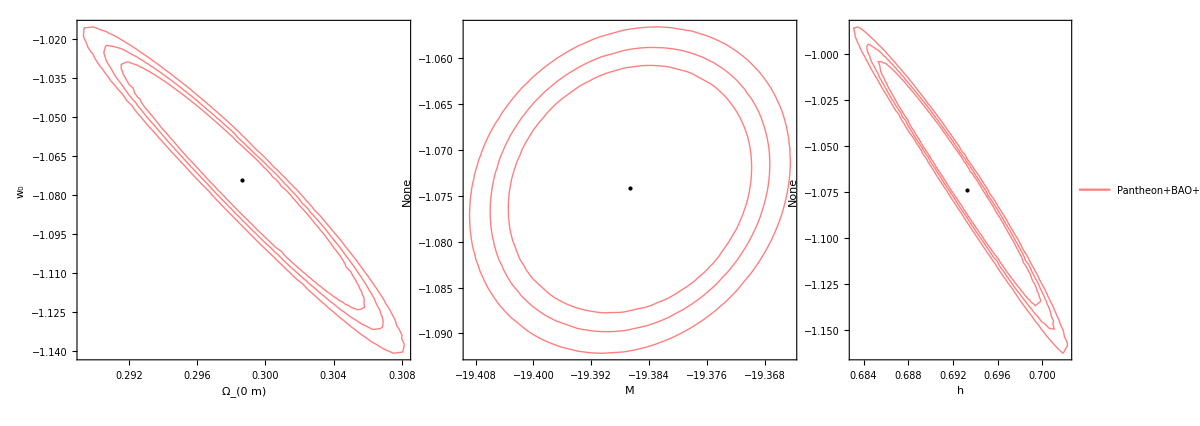

```mathematica
fig8=GraphicsGrid[{{plt4,plt5,plt6}},Spacings->-35,ImageSize->1200]
```

## wwcdm

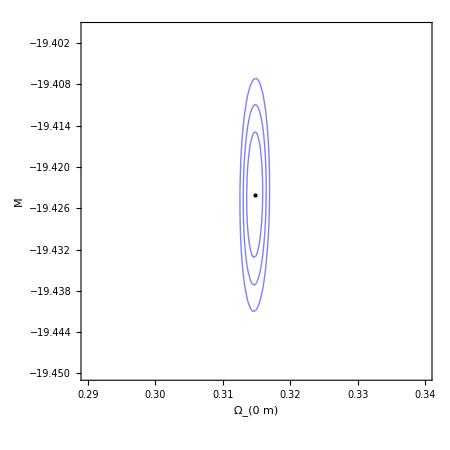

```mathematica
contour7 =ContourPlot[chi2total[M,om,wowwcdm,wawwcdm,hwwcdm],{om,0.29,0.34},{M,-19.4,-19.45},Contours->{minwwcdm[[1]]+dchi[1,4],minwwcdm[[1]]+dchi[2,4],minwwcdm[[1]]+dchi[3,4]},FrameLabel->{"Ω_(0  m)","M"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{omwwcdm,Mwwcdm}]}},ContourShading->False,ContourStyle->Blue,ImageSize->450]
```

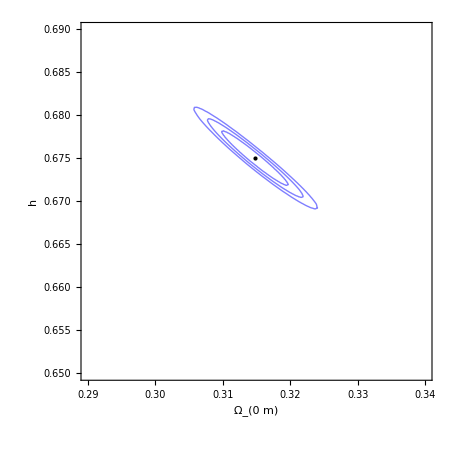

```mathematica
contour8 =ContourPlot[chi2total[Mwwcdm,om,wowwcdm,wawwcdm,h],{om,0.29,0.34},{h,0.65,0.69},Contours->{minwwcdm[[1]]+dchi[1,4],minwwcdm[[1]]+dchi[2,4],minwwcdm[[1]]+dchi[3,4]},FrameLabel->{"Ω_(0  m)","h"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{omwwcdm,hwwcdm}]}},ContourShading->False,ContourStyle->Blue,ImageSize->450]
```

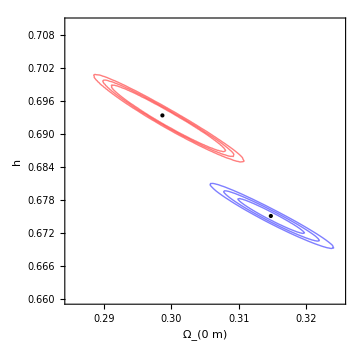

```mathematica
plt8 = Show[contour2,contour8,PlotRange->{{0.285,0.325},{0.66,0.71}},AspectRatio->1,PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Frame->{{True,True},{True,True}},Epilog->{{PointSize[Large],Black,Point[{omwwcdm,hwwcdm}]},{PointSize[Large],Black,Point[{omwcdm,hwcdm}]}}]
```

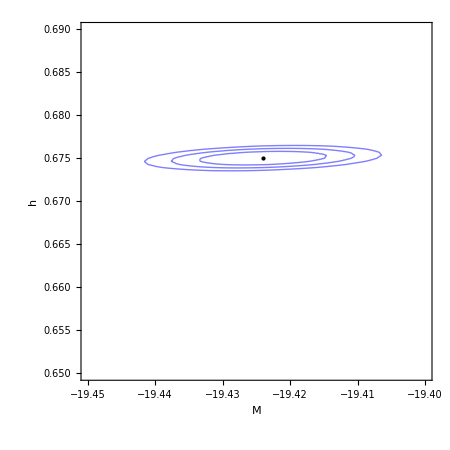

```mathematica
contour9 =ContourPlot[chi2total[M,omwwcdm,wowwcdm,wawwcdm,h],{M,-19.4,-19.45},{h,0.65,0.69},Contours->{minwwcdm[[1]]+dchi[1,4],minwwcdm[[1]]+dchi[2,4],minwwcdm[[1]]+dchi[3,4]},FrameLabel->{"M","h"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{Mwwcdm,hwwcdm}]}},ContourShading->False,ContourStyle->Blue,ImageSize->450]
```

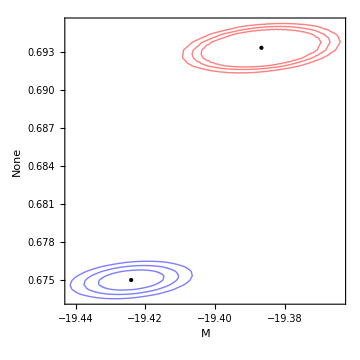

```mathematica
plt9 = Show[contour3,contour9,PlotRange->{{-19.35,-19.45},{0.66,0.71}},AspectRatio->1,Frame->{{False,True},{True,True}},FrameLabel->{"M","None"},PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImagePadding->{{Automatic, 50}, {Automatic, 25}},Epilog->{{PointSize[Large],Black,Point[{Mwwcdm,hwwcdm}]},{PointSize[Large],Black,Point[{Mwcdm,hwcdm}]}}]
```

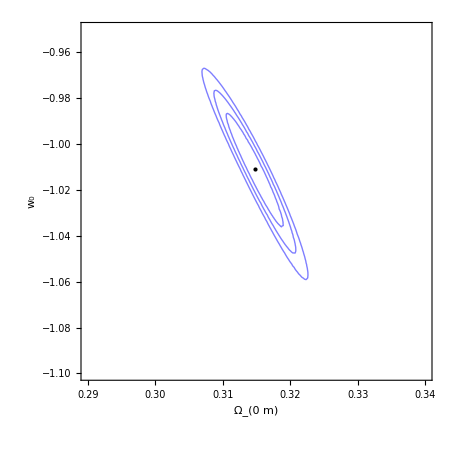

```mathematica
contour10 =ContourPlot[chi2total[Mwwcdm,om,w0,wawwcdm,hwwcdm],{om,0.29,0.34},{w0,-1.10,-0.95},Contours->{minwwcdm[[1]]+dchi[1,4],minwwcdm[[1]]+dchi[2,4],minwwcdm[[1]]+dchi[3,4]},FrameLabel->{"Ω_(0  m)","w_0"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{omwwcdm,wowwcdm}]}},ContourShading->False,ContourStyle->Blue,ImageSize->450]
```

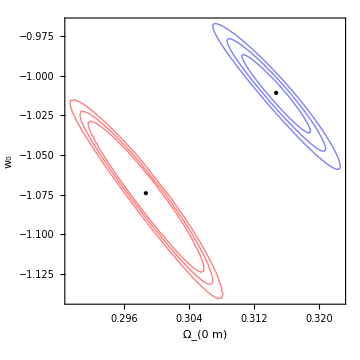

```mathematica
plt10 = Show[contour4,contour10,PlotRange->{{0.28,0.325},{-0.95,-1.25}},AspectRatio->1,PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Frame->{{True,True},{True,True}},Epilog->{{PointSize[Large],Black,Point[{omwwcdm,wowwcdm}]},{PointSize[Large],Black,Point[{omwcdm,wowcdm}]}},ImagePadding->{{80,Automatic}, {53, 40}}]
```

```mathematica
|
```

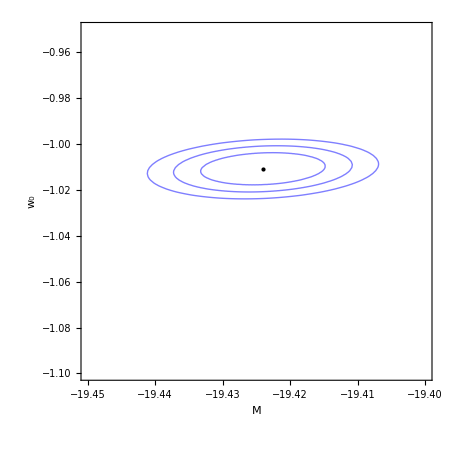

```mathematica
contour11 =ContourPlot[chi2total[M,omwwcdm,w0,wawwcdm,hwwcdm],{M,-19.4,-19.45},{w0,-1.10,-0.95},Contours->{minwwcdm[[1]]+dchi[1,4],minwwcdm[[1]]+dchi[2,4],minwwcdm[[1]]+dchi[3,4]},FrameLabel->{"M","w_0"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{Mwwcdm,wowwcdm}]}},ContourShading->False,ContourStyle->Blue,ImageSize->450]
```

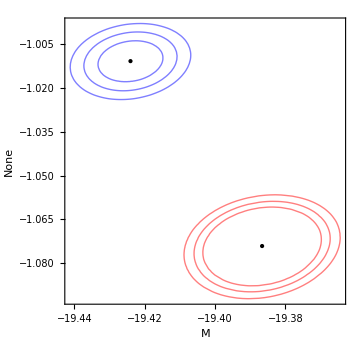

```mathematica
plt11 = Show[contour5,contour11,PlotRange->{{-19.35,-19.45},{-0.95,-1.25}},AspectRatio->1,Frame->{{False,True},{True,True}},FrameLabel->{"M","None"},PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImagePadding->{{Automatic, Automatic}, {Automatic,40}},Epilog->{{PointSize[Large],Black,Point[{Mwwcdm,wowwcdm}]},{PointSize[Large],Black,Point[{Mwcdm,wowcdm}]}}]
```

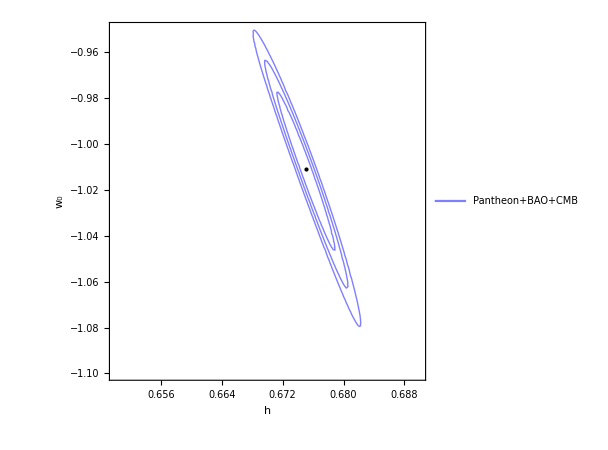

```mathematica
contour12 =ContourPlot[chi2total[Mwwcdm,omwwcdm,w0,wawwcdm,h],{h,0.65,0.69},{w0,-1.10,-0.95},Contours->{minwwcdm[[1]]+dchi[1,4],minwwcdm[[1]]+dchi[2,4],minwwcdm[[1]]+dchi[3,4]},FrameLabel->{"h","w_0"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{hwwcdm,wowwcdm}]}},ContourShading->False,ContourStyle->Blue,ImageSize->450,PlotLegends->Placed[{"Pantheon+BAO+CMB"},{Right,Bottom}]]
```

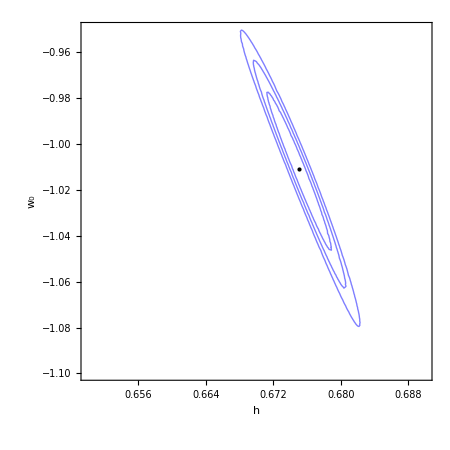

```mathematica
contour12b =ContourPlot[chi2total[Mwwcdm,omwwcdm,w0,wawwcdm,h],{h,0.65,0.69},{w0,-1.10,-0.95},Contours->{minwwcdm[[1]]+dchi[1,4],minwwcdm[[1]]+dchi[2,4],minwwcdm[[1]]+dchi[3,4]},FrameLabel->{"h","w_0"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Epilog->{{PointSize[Large],Black,Point[{hwwcdm,wowwcdm}]}},ContourShading->False,ContourStyle->Blue,ImageSize->450]
```

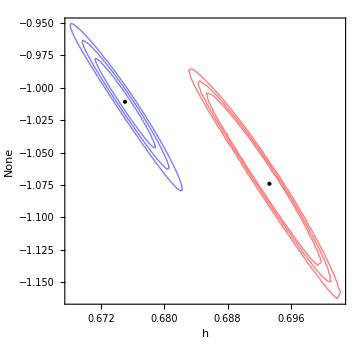

```mathematica
plt12 = Show[contour12,contour6,PlotRange->{{0.665,0.72},{-0.95,-1.25}},AspectRatio->1,Frame->{{False,True},{True,True}},FrameLabel->{"h","None"},PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImagePadding->{{Automatic, 90}, {Automatic, 40}},Epilog->{{PointSize[Large],Black,Point[{hwwcdm,wowwcdm}]},{PointSize[Large],Black,Point[{hwcdm,wowcdm}]}}]
```

```mathematica
c1 = Plot[{-19.207,-19.281},{x,-1,1},PlotStyle->Opacity[0.1],Filling->{1->{2}},FillingStyle->Directive[Opacity[0.3],Gray]];
c2 = Plot[{-19.373,-19.427},{x,-1,1},PlotStyle->Opacity[0.1],Filling->{1->{2}},FillingStyle->Directive[Opacity[0.3],Gray]];
```

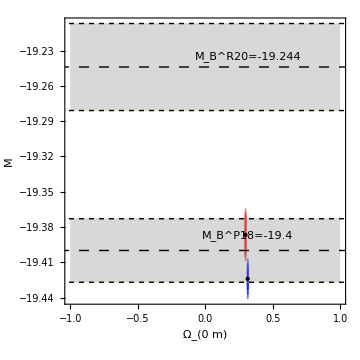

```mathematica
plt7 = Show[contour1,contour7,c1,c2,PlotRange->{{0.28,0.325},{-19.20,-19.45}},Epilog->{Text["M_B^P18=-19.4",{0.315,-19.387}],{Dashing[0.02],Line[{{-30,-19.4},{8,-19.4}}]},{Dashing[0.01],Line[{{-30,-19.373},{8,-19.373}}]},{Dashing[0.01],Line[{{-30,-19.427},{8,-19.427}}]},{Dashing[0.02],Line[{{-30,-19.244},{8,-19.244}}]},{Dashing[0.01],Line[{{-30,-19.281},{8,-19.281}}]},{Dashing[0.01],Line[{{-30,-19.207},{8,-19.207}}]},Text["M_B^R20=-19.244",{0.315,-19.235}],{PointSize[Medium],Black,Point[{omwwcdm,Mwwcdm}]},{PointSize[Medium],Black,Point[{omwcdm,Mwcdm}]}},AspectRatio->1,PlotRangeClipping->True,ImageSize->Medium]
```

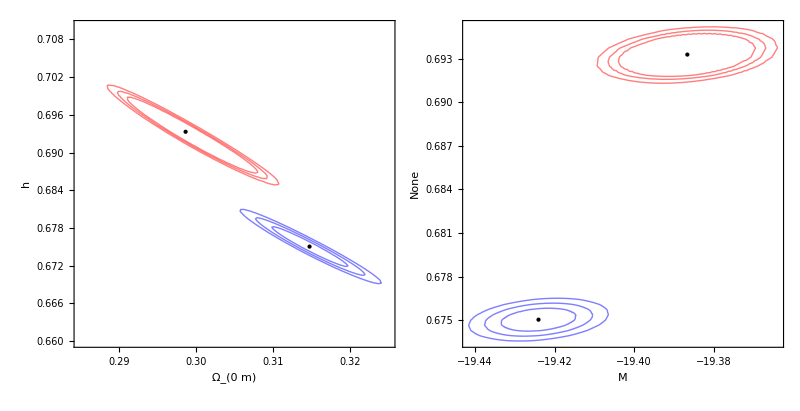

```mathematica
fig12 = GraphicsGrid[{{plt8,plt9}},Spacings->-20,ImageSize->800]
```

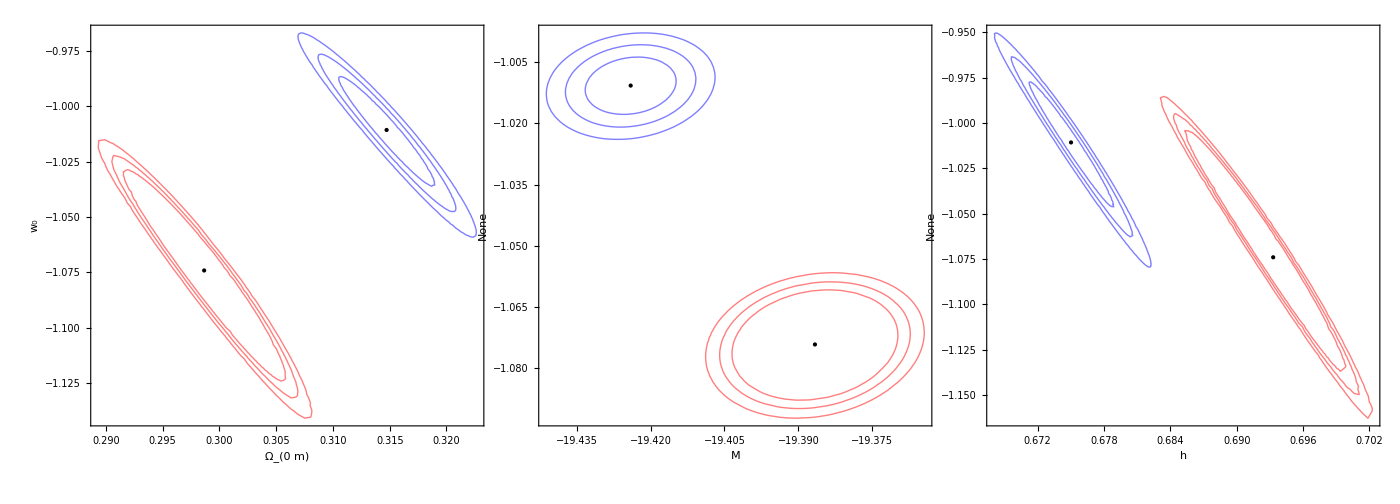

```mathematica
fig13 = GraphicsGrid[{{plt10,plt11,plt12}},Spacings->-40,ImageSize->1400]
```

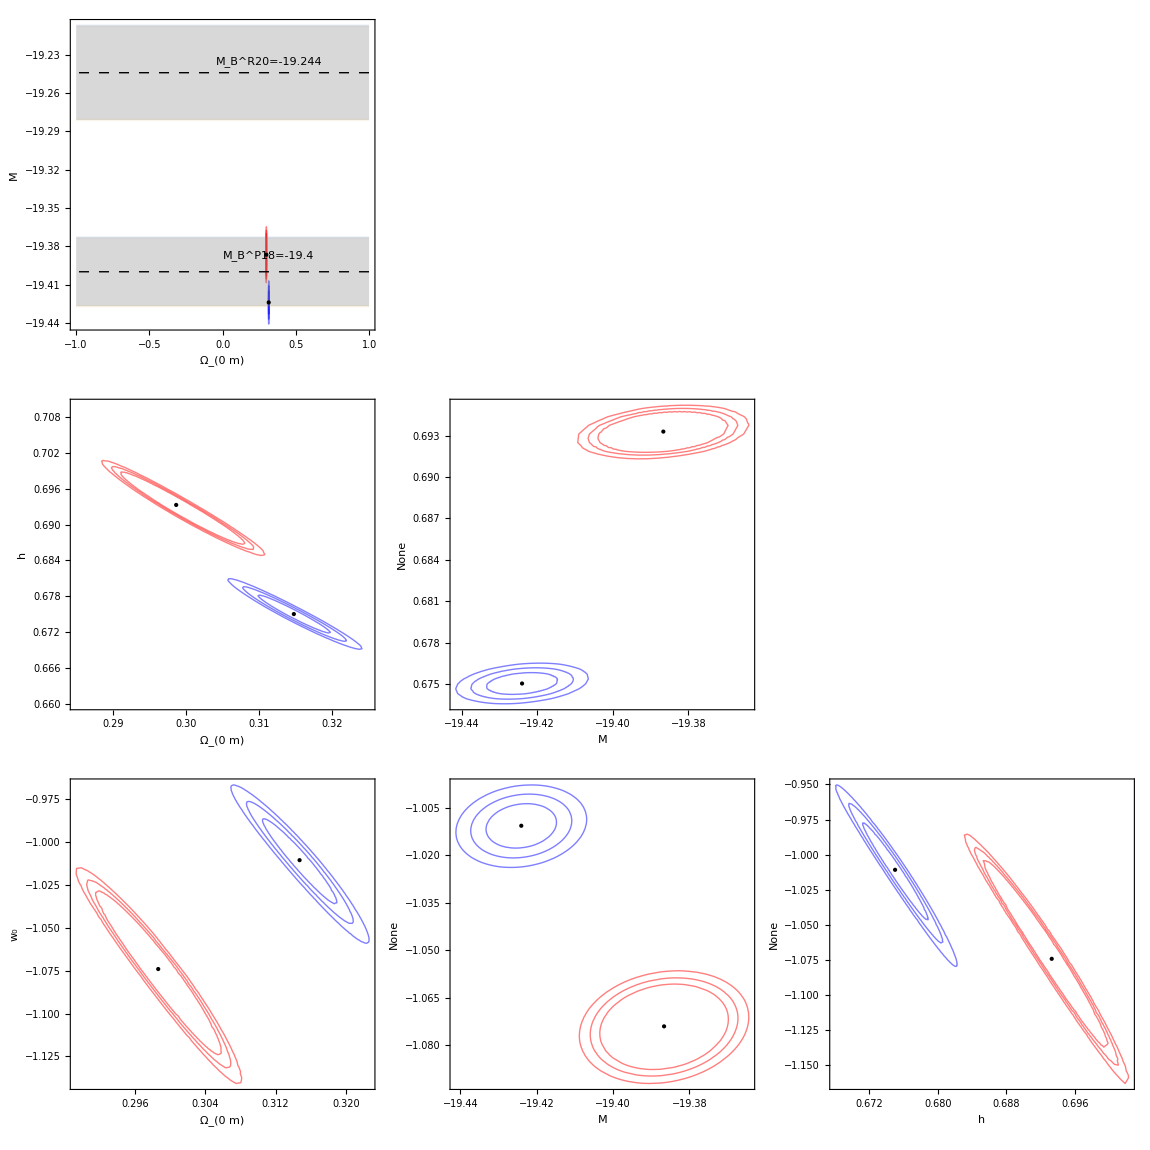

```mathematica
fig4=GraphicsGrid[{{plt7},{plt8,plt9},{plt10,plt11,plt12}},Spacings->-10,ImageSize->1150]
```

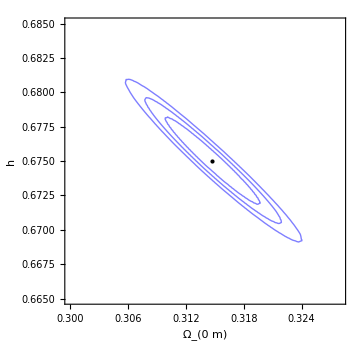

```mathematica
plt14 = Show[contour8,PlotRange->{{0.30,0.328},{0.665,0.685}},AspectRatio->1,PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Frame->{{True,True},{True,True}}]
```

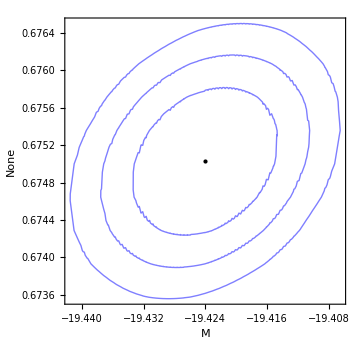

```mathematica
plt15 = Show[contour9,PlotRange->{{-19.395,-19.454},{0.665,0.685}},AspectRatio->1,Frame->{{False,True},{True,True}},FrameLabel->{"M","None"},PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImagePadding->{{Automatic, 50}, {Automatic, 25}}]
```

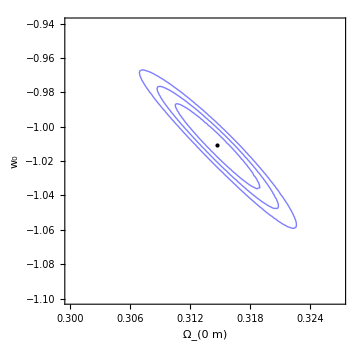

```mathematica
plt16 = Show[contour10,PlotRange->{{0.3,0.327},{-1.10,-0.94}},AspectRatio->1,PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],Frame->{{True,True},{True,True}}]
```

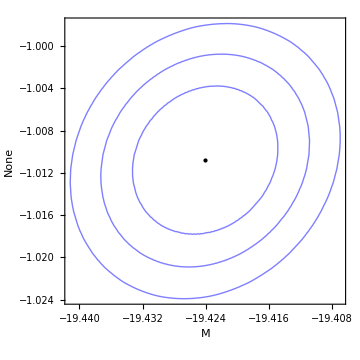

```mathematica
plt17 = Show[contour11,PlotRange->{{-19.395,-19.454},{-1.10,-0.94}},AspectRatio->1,Frame->{{False,True},{True,True}},FrameLabel->{"M","None"},PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImagePadding->{{Automatic, Automatic}, {Automatic, 10}}]
```

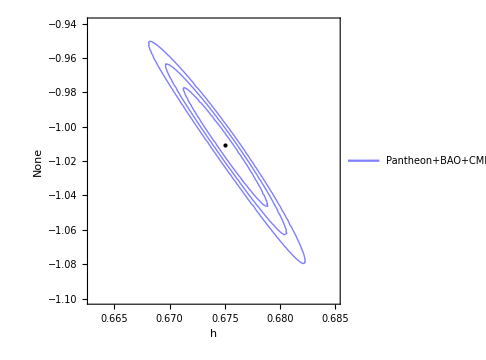

```mathematica
plt18 = Show[contour12,PlotRange->{{0.663,0.685},{-1.10,-0.94}},AspectRatio->1,Frame->{{False,True},{True,True}},FrameLabel->{"h","None"},PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImagePadding->{{Automatic, 60}, {Automatic, 40}}]
```

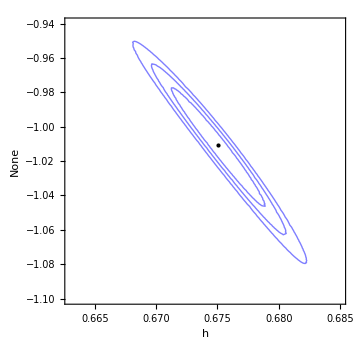

```mathematica
plt18b = Show[contour12b,PlotRange->{{0.663,0.685},{-1.10,-0.94}},AspectRatio->1,Frame->{{False,True},{True,True}},FrameLabel->{"h","None"},PlotRangeClipping->True,ImageSize->Medium,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImagePadding->{{Automatic, 60}, {Automatic, 40}}]
```

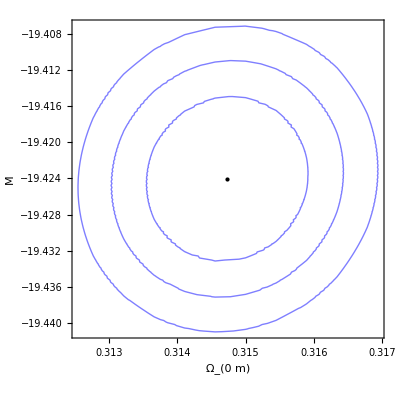

```mathematica
plt13 = Show[contour7,PlotRange->{{0.31,0.318},{-19.40,-19.45}},AspectRatio->1,PlotRangeClipping->True,ImageSize->400]
```

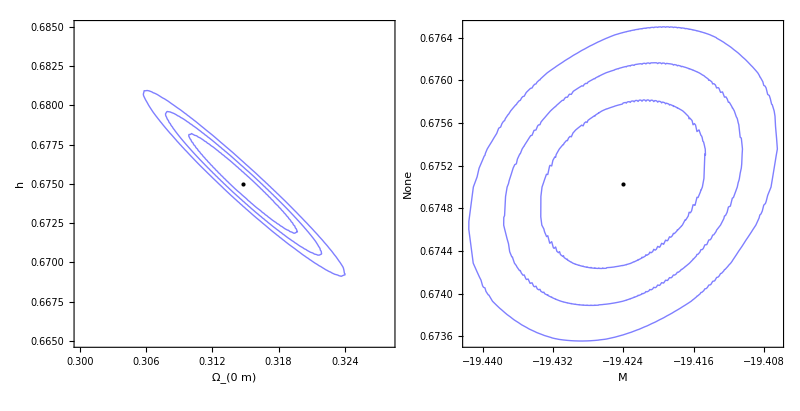

```mathematica
fig9=GraphicsGrid[{{plt14,plt15}},Spacings->-20,ImageSize->800]
```

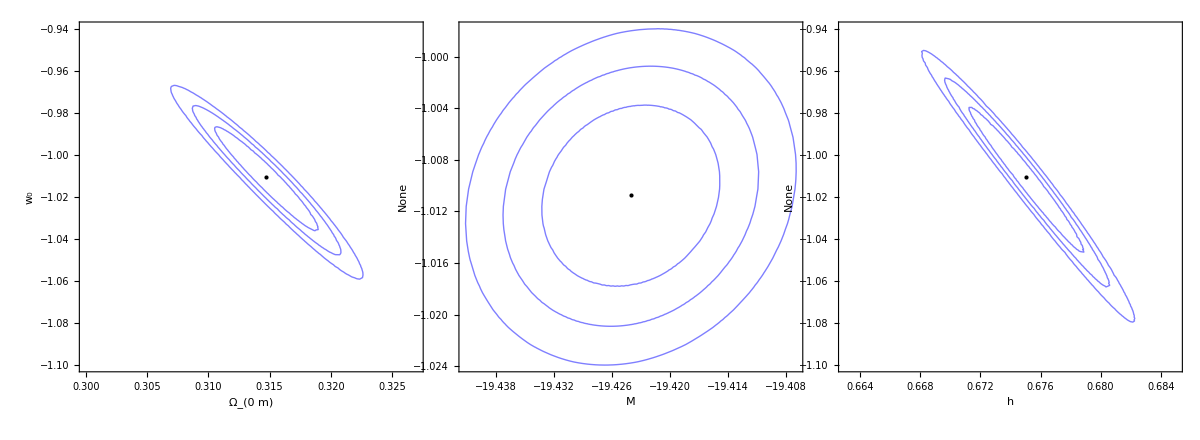

```mathematica
fig10=GraphicsGrid[{{plt16,plt17,plt18b}},Spacings->-50,ImageSize->1200]
```